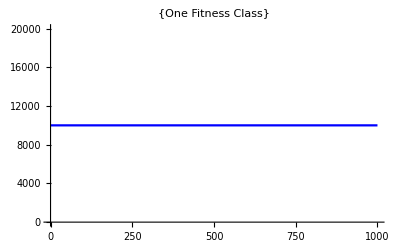

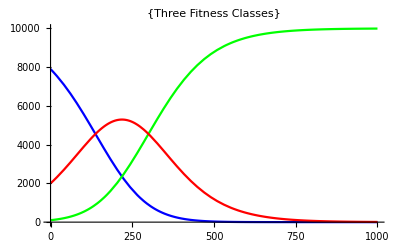

```mathematica
(* Testing SystemSolver, SolveDiffEqs *)
Δc1=0.01;
Δc2=0.02;
popsize=10^4;
timestep=1000; 
(* Testing system solver for one fitness class *)
genotypes={{1,1}};
genotypeabundances={10^4};
{system,sol}=SolveDiffEqs[popsize,Δc1,Δc2,genotypeabundances,genotypes,timestep];
Plot[{n1[t]/.sol[[1]]},{t,0,timestep},PlotStyle->{Blue},PlotLabel->{"One Fitness Class"}]
(* Testing system solver for three fitness class *)
genotypes={{1,1},{1,2},{2,1}};
genotypeabundances={10^4-100-2000,100,2000};
{system,sol}=SolveDiffEqs[popsize,Δc1,Δc2,genotypeabundances,genotypes,timestep];
Plot[{n1[t]/.sol[[1]],n2[t]/.sol[[1]],n3[t]/.sol[[1]]},{t,0,timestep},PlotStyle->{Blue,Green,Red},PlotLabel->{"Three Fitness Classes"}]
```

```mathematica
(* Testing module that gets new mutants at boundary, getNextMutants *)
genotypes={{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}}
newmutantgenotypes=getNextMutants[genotypes]
```

{{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}}

{{{4,1},{{6,1}},0,0},{{3,2},{{5,1},{6,2}},0,0},{{2,3},{{3,1},{5,2}},0,0},{{1,4},{{3,2}},0,0}}

```mathematica
(* Testing module that checks for new mutations, NextMutation *)
Δc1=0.01;
Δc2=0.02;
U1=2 10^-4;
U2=1 10^-4;
popsize=10^6;
starttime=0;
timestep=100; 
r=0.5;
genotypes={{1,1},{1,2},{1,3},{2,1},{2,2},{3,1}};
genotypeabundances=Table[popsize ((r-1)/(r^Length[genotypes]-1))r^(i-1),{i,1,Length[genotypes]}];
```

```mathematica
{sol,system}=SolveDiffEqs[popsize,Δc1,Δc2,genotypeabundances,genotypes,timestep];
```

```mathematica
NextMutation[popsize,Δc1,Δc2,U1,U2,sol,genotypes,starttime,timestep]
```

ReplaceAll::reps: {n1'[t]==n1[t] (1.03+(-1.03 n1[«1»]-1.05 n2[«1»]-1.07 n3[«1»]-1.04 n4[«1»]-1.06 n5[«1»]-1.05 n6[«1»])/1000000)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolveValue::underdet: There are more dependent variables, {n1[t],n2[t],n3[t],n4[t],n5[t],n6[t],y[t]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {n1'[t]==n1[t] (1.03+(-1.03 n1[«1»]-1.05 n2[«1»]-1.07 n3[«1»]-1.04 n4[«1»]-1.06 n5[«1»]-1.05 n6[«1»])/1000000)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolveValue::underdet: There are more dependent variables, {n1[t],n2[t],n3[t],n4[t],n5[t],n6[t],y[t]}, than equations, so the system is underdetermined.

ReplaceAll::reps: {n1'[t]==n1[t] (1.03+(-1.03 n1[«1»]-1.05 n2[«1»]-1.07 n3[«1»]-1.04 n4[«1»]-1.06 n5[«1»]-1.05 n6[«1»])/1000000)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolveValue::underdet: There are more dependent variables, {n1[t],n2[t],n3[t],n4[t],n5[t],n6[t],y[t]}, than equations, so the system is underdetermined.

General::stop: Further output of NDSolveValue::underdet will be suppressed during this calculation.

{0,{{{4,1},{{6,1}},0,0.837611},{{3,2},{{5,1},{6,2}},0,0.790149},{{2,3},{{3,1},{5,2}},0,0.824157},{{1,4},{{3,2}},0,2.44103}},0.240337<If[1.06-((1.03 n1[0]+1.05 n2[0]+1.07 n3[0]+1.04 n4[0]+1.06 n5[0]+1.05 n6[0])/1000000/.n1'[0]==n1[0] (1.03+(-1.03 n1[0]-1.05 n2[0]-1.07 n3[0]-1.04 n4[0]-1.06 n5[0]-1.05 n6[0])/1000000))>0,(1+{4,1}⟦1⟧ 0.01+{4,1}⟦2⟧ 0.02-((1.03 n1[0]+1.05 n2[0]+1.07 n3[0]+1.04 n4[0]+1.06 n5[0]+1.05 n6[0])/1000000/.n1'[0]==n1[0] (1.03+(-1.03 n1[0]-1.05 n2[0]-1.07 n3[0]-1.04 n4[0]-1.06 n5[0]-1.05 n6[0])/1000000)))/(2+{4,1}⟦1⟧ 0.01+{4,1}⟦2⟧ 0.02-((1.03 n1[0]+1.05 n2[0]+1.07 n3[0]+1.04 n4[0]+1.06 n5[0]+1.05 n6[0])/1000000/.n1'[0]==n1[0] (1.03+(-1.03 n1[0]-1.05 n2[0]-1.07 n3[0]-1.04 n4[0]-1.06 n5[0]-1.05 n6[0])/1000000))),0],If[1.06-((1.03 n1[0]+1.05 n2[0]+1.07 n3[0]+1.04 n4[0]+1.06 n5[0]+1.05 n6[0])/1000000/.n1'[0]==n1[0] (1.03+(-1.03 n1[0]-1.05 n2[0]-1.07 n3[0]-1.04 n4[0]-1.06 n5[0]-1.05 n6[0])/1000000))>0,(1+{4,1}⟦1⟧ 0.01+{4,1}⟦2⟧ 0.02-((1.03 n1[0]+1.05 n2[0]+1.07 n3[0]+1.04 n4[0]+1.06 n5[0]+1.05 n6[0])/1000000/.n1'[0]==n1[0] (1.03+(-1.03 n1[0]-1.05 n2[0]-1.07 n3[0]-1.04 n4[0]-1.06 n5[0]-1.05 n6[0])/1000000)))/(2+{4,1}⟦1⟧ 0.01+{4,1}⟦2⟧ 0.02-((1.03 n1[0]+1.05 n2[0]+1.07 n3[0]+1.04 n4[0]+1.06 n5[0]+1.05 n6[0])/1000000/.n1'[0]==n1[0] (1.03+(-1.03 n1[0]-1.05 n2[0]-1.07 n3[0]-1.04 n4[0]-1.06 n5[0]-1.05 n6[0])/1000000))),0],parentfitclassindices$6062}